```mathematica
test630=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\1000umclistaltalt.txt","Table"];
```

```mathematica
test6300=test630[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]=Round[test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]];
```

```mathematica
test6300[[2;;Length[test6300],{8}]]=N[test6300[[2;;Length[test6300],{8}]]-750];
```

```mathematica
test6300[[2;;Length[test6300],{10}]]=N[test6300[[2;;Length[test6300],{10}]]-963];
```

```mathematica
test6300[[2;;Length[test6300],{3}]]=N[test6300[[2;;Length[test6300],{3}]]*1/60];
```

```mathematica
test6300cut=removefljumps[test6300];
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

```mathematica
linstest6300cut=lineagefinder[test6300cut];//AbsoluteTiming
```

{9.66533,Null}

```mathematica
comblintest630=combinelineages2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{17.1144,Null}

```mathematica
comblinmultiplytest630=combinelineagesmulitply2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{16.3452,Null}

```mathematica
growthtest630noextrap=growthratecalcsupnoextrap[comblinmultiplytest630,30,comblintest630];//AbsoluteTiming
```

387

{3.58861,Null}

```mathematica
testset=RandomChoice[Table[i,{i,1,320}],50]
```

{252,65,293,172,148,114,31,74,216,287,225,34,120,164,156,160,261,29,150,202,160,203,148,277,137,14,40,191,174,224,43,210,46,214,104,93,187,268,149,286,171,184,4,93,120,112,23,223,208,119}

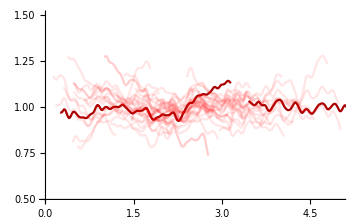

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,{313,123}],PlotRange->{{0,5},{0.5,1.5}},PlotStyle->Darker[Red],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],Red]]}]
```

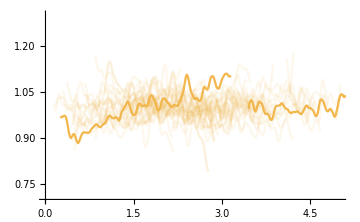

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,{313,123}],PlotRange->{{0,5},{0.7,1.3}},PlotStyle->RGBColor["#f2b74d"],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],RGBColor["#f2b74d"]]]}]
```

```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
metabsim=metabgensteadystate[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{472.106,Null}

```mathematica
keepMetabSS=keepallmetabmaintainsteadystate[metabsim[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1181.14,Null}

```mathematica
metabsimMemory=metabproteinmemfast[keepMetabSS];
```

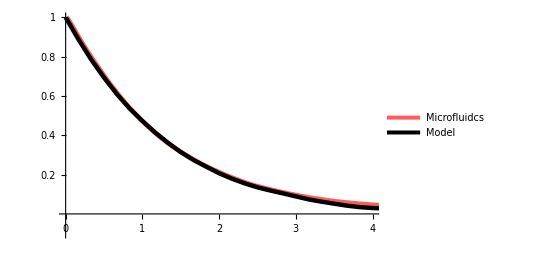

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1mmmcACF30minwindowsmooth]}],iptg1mmmcACF30minwindowsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[1]]]},PlotRange->{{0,4},{-.1,1}},PlotLegends->Placed[{"Microfluidcs","Model"},Right],PlotStyle->{{Thickness[0.008],RGBColor[1,0.36,0.36]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
{iptg1000um630growthACFsmooth,iptg1000um630mcACFsmooth,iptg1000um630betaxACFsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1000um630ACFsmooth.txt","Table"];
```

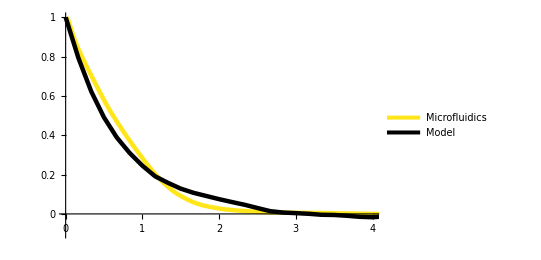

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1000um630betaxACFsmooth]}],iptg1000um630betaxACFsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[3]]]},PlotRange->{{0,4},{-.1,1}},
PlotLegends->Placed[{"Microfluidics","Model"},Right],
PlotStyle->{{Thickness[0.008],RGBColor[1,0.9,0.1]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0,0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
exp227rawdata=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{1.33559,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{21.5147,Null}

```mathematica
combliniptg1mm=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{59.0616,Null}

```mathematica
lowprodmc=Join[combliniptg1mm[[180]][[77;;Length[combliniptg1mm[[180]]],6]],combliniptg1mm[[181]][[All,6]]];
```

```mathematica
lowprodbx=Join[combliniptg1mm[[180]][[77;;Length[combliniptg1mm[[180]]],7]],combliniptg1mm[[181]][[All,7]]];
```

```mathematica
midprodmc=Join[combliniptg1mm[[84]][[29;;Length[combliniptg1mm[[84]]],6]],combliniptg1mm[[85]][[All,6]]];
```

```mathematica
midprodbc=Join[combliniptg1mm[[84]][[29;;Length[combliniptg1mm[[84]]],7]],combliniptg1mm[[85]][[All,7]]];
```

```mathematica
highprodmc=combliniptg1mm[[100]][[All,6]];
```

```mathematica
highprodbx=combliniptg1mm[[100]][[All,7]];
```

```mathematica
Mean[lowprodmc]
```

2392.36

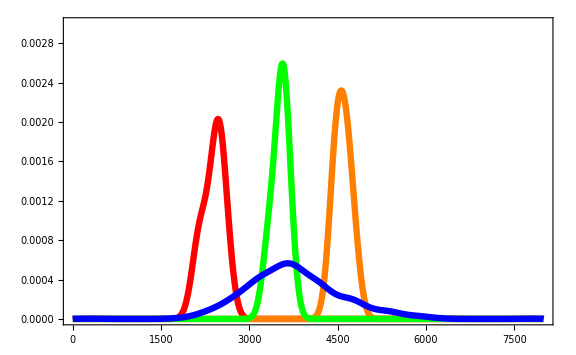

```mathematica
Show[{SmoothHistogram[{lowprodmc,midprodmc,highprodmc},100,PlotRange->{{0,8000},{0,0.003}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,True,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,6]](*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],200,PlotRange->{{0,8000},{0,0.003}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,True,False,False},FrameStyle->Directive[Black,25]]}]
```

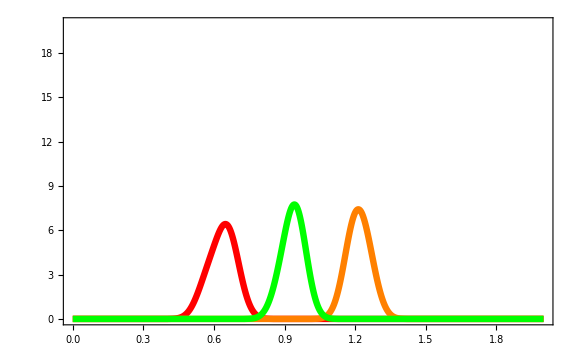
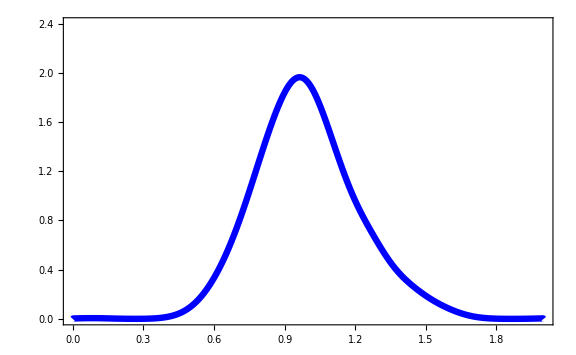

```mathematica
Show[{SmoothHistogram[{lowprodmc/3770,midprodmc/3770,highprodmc/3770},0.04,PlotRange->{{0,2},{0,20}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,6]]/3770(*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],0.08,PlotRange->{{0,2},{0,2.4}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False,False},FrameStyle->Directive[Black,25]]}]
```

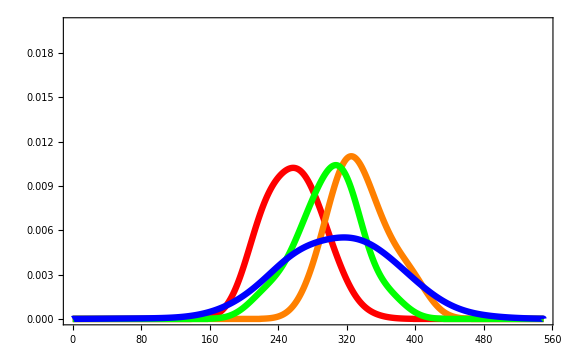

```mathematica
Show[{SmoothHistogram[Map[combliniptg1mm[[#]][[All,7]]&,{180,84,100}],20,PlotRange->{{0,550},{0,0.02}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,True,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,7]](*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],30,PlotRange->{{0,550},{0,0.02}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]]}]
```

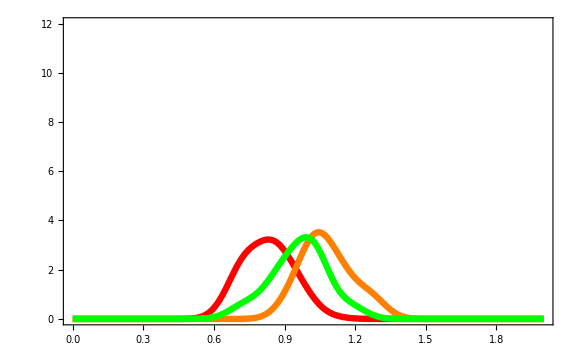
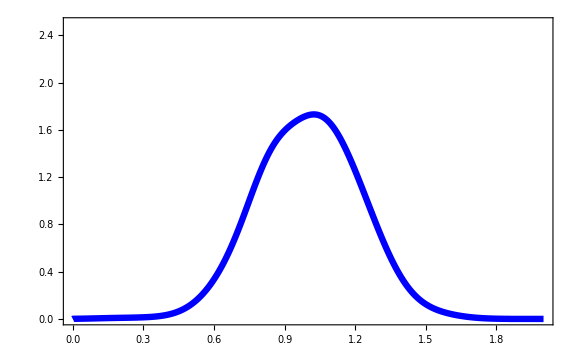

```mathematica
Overlay[{SmoothHistogram[Map[combliniptg1mm[[#]][[All,7]]/311&,{180,84,100}],0.06,PlotRange->{{0,2},{0,12}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,7]]/311(*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],0.09,PlotRange->{{0,2},{0,2.5}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False,False},FrameStyle->Directive[Black,25]]}]
```

```mathematica
Allbeta=Map[combliniptg1mm[[#]][[1,7]]&,Table[i,{i,Length[combliniptg1mm]}]];
```

```mathematica
Mean[Allbeta]
```

311.133

```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\2022-2023\\microfluidic\\modeling files\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
GRbxCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmbetaxgrowthCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmbetaxgrowthCCCF30minwindowsmooth]-1)/2}],iptg1mmbetaxgrowthCCCF30minwindowsmooth};
```

```mathematica
GRmcCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmmcgrowthCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmmcgrowthCCCF30minwindowsmooth]-1)/2}],iptg1mmmcgrowthCCCF30minwindowsmooth};
```

```mathematica
mcbxCCF227smooth=Transpose@{Table[(i/60),{i,-(Length[iptg1mmmcbetaxCCCF30minwindowsmooth]-1)/2,(Length[iptg1mmmcbetaxCCCF30minwindowsmooth]-1)/2}],iptg1mmmcbetaxCCCF30minwindowsmooth};
```

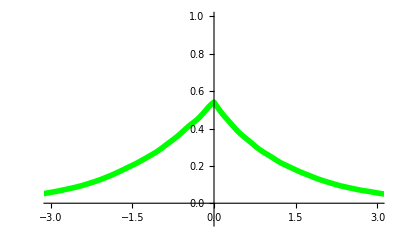

```mathematica
ListLinePlot[{mcbxCCF227smooth},PlotRange->{{-3,3},{-.1,1}},PlotStyle->{Directive[Thickness[0.01],Green]},AxesStyle->Directive[Black, 16]]
```

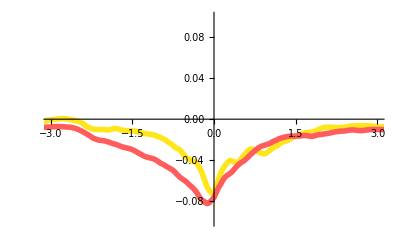

```mathematica
ListLinePlot[{GRbxCCF227smooth,GRmcCCF227smooth},PlotRange->{{-3,3},{-.1,0.1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.9,0.1]],Directive[Thickness[0.01],RGBColor[1,0.36,0.36]]},AxesStyle->Directive[Black, 16]]
```

```mathematica
exp227transition=highlowtransitionovertime[comblinexp227];
```

```mathematica
exp630transition=highlowtransitionovertime[comblinexp630];
```

```mathematica
avg=N[Mean[{100*exp630transition[[1]],100*exp227transition[[1]]}]]
```

{{100.,0.,0.},{85.9551,14.0449,0.},{76.3808,23.6192,0.},{65.4791,34.5209,0.},{52.4107,47.5893,0.},{46.2847,53.7153,0.},{45.3998,54.6002,0.},{45.3998,54.1578,0.442478}}

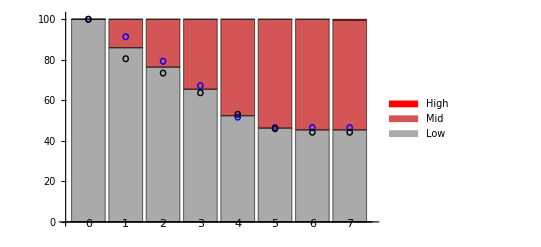

```mathematica
(*Define data and errors*)

(*Compute cumulative heights for stacking*)


(*Generate the stacked bar chart*)
bars=BarChart[avg,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Red},.5],Red},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}];

(*Generate error bar graphics*)
errorGraphics=Graphics[Table[With[{x=i,yset1=N[100*exp630transition[[1,All,1]]][[i]],yset2=N[100*exp227transition[[1,All,1]]][[i]]},{{Blue,Circle[{x,yset1},{0.07,1.4}]},{Black,Circle[{x,yset2},{0.07,1.4}]}}],{i,Length[avg]}]
];

(*Combine the bar chart with error bars*)
Show[bars,errorGraphics]
```

```mathematica
avghigh=N[Mean[{100*exp630transition[[2]],100*exp227transition[[2]]}]]
```

{{0.,0.,100.},{0.,16.2016,83.7984},{0.,30.6279,69.3721},{0.,41.7287,58.2713},{0.,58.8682,41.1318},{2.,67.969,30.031},{2.77519,74.9457,22.2791},{4.32558,76.1085,19.5659}}

```mathematica
barshigh=BarChart[avghigh,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Red},.5],Red},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}];
```

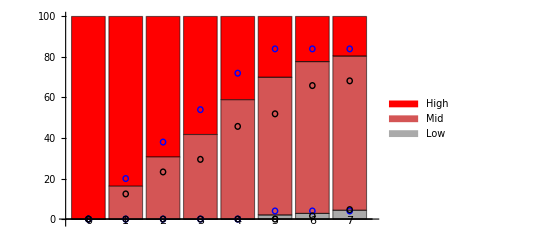

```mathematica
errorGraphicshigh=Graphics[Table[With[{x=i,ymid630=N[100*exp630transition[[2,All,2]]][[i]],ymid227=N[100*exp227transition[[2,All,2]]][[i]],ylow630=N[100*exp630transition[[2,All,1]]][[i]],ylow227=N[100*exp227transition[[2,All,1]]][[i]]},
{{Blue,Circle[{x,ymid630},{0.07,1.4}]},{Blue,Circle[{x,ylow630},{0.07,1.4}]},{Black,Circle[{x,ymid227},{0.07,1.4}]},{Black,Circle[{x,ylow227},{0.07,1.4}]}}],{i,Length[avg]}]
];


(*Combine the bar chart with error bars*)
Show[barshigh,errorGraphicshigh]
```

```mathematica
avgyfp=N[Mean[{100*exp630transition[[3]],100*exp227transition[[3]]}]]
```

{{100.,0.,0.},{72.6601,25.2189,2.12096},{56.4313,40.2573,3.31144},{32.5123,63.3826,4.10509},{21.1823,67.8845,10.9332},{8.867,78.2157,12.9174},{4.4335,81.4587,14.1078},{4.03667,81.4587,14.5047}}

```mathematica
N[100*exp630transition[[3,All,3]]]
```

{0.,3.44828,3.44828,3.44828,15.5172,15.5172,15.5172,15.5172}

```mathematica
N[100*exp630transition[[3,All,2]]]+N[100*exp630transition[[3,All,1]]]
```

{100.,96.5517,96.5517,96.5517,84.4828,84.4828,84.4828,84.4828}

```mathematica
N[100*exp630transition[[3,All,1]]]
```

{100.,81.0345,62.069,29.3103,13.7931,3.44828,1.72414,1.72414}

```mathematica
baryfplow=BarChart[avgyfp,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Yellow},.5],Yellow},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}];
```

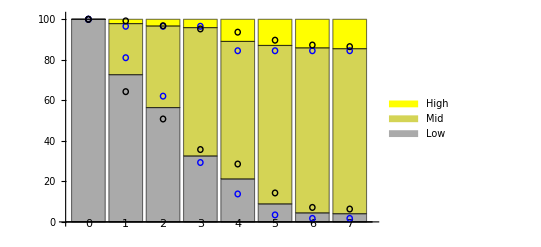

```mathematica
errorGraphicsyfplow=Graphics[Table[With[{x=i,ymid630=N[100*exp630transition[[3,All,2]]][[i]]+N[100*exp630transition[[3,All,1]]][[i]],ymid227=N[100*exp227transition[[3,All,2]]][[i]]+N[100*exp227transition[[3,All,1]]][[i]],ylow630=N[100*exp630transition[[3,All,1]]][[i]],ylow227=N[100*exp227transition[[3,All,1]]][[i]]},
{{Blue,Circle[{x,ymid630},{0.07,1.4}]},{Blue,Circle[{x,ylow630},{0.07,1.4}]},{Black,Circle[{x,ymid227},{0.07,1.4}]},{Black,Circle[{x,ylow227},{0.07,1.4}]}}],{i,Length[avg]}]
];



(*Combine the bar chart with error bars*)
Show[baryfplow,errorGraphicsyfplow]
```

```mathematica
avgyfplow=N[Mean[{100*exp630transition[[4]],100*exp227transition[[4]]}]]
```

{{0.,0.,100.},{3.40909,36.9697,59.6212},{10.6061,44.0909,45.303},{13.0303,52.5758,34.3939},{13.7879,64.4697,21.7424},{15.8333,76.2121,7.95455},{15.8333,81.8939,2.27273},{16.5909,81.5152,1.89394}}

```mathematica
N[100*exp630transition[[4,All,3]]]
```

{100.,70.,46.6667,31.6667,11.6667,0.,0.,0.}

```mathematica
N[100*exp630transition[[4,All,2]]]+N[100*exp630transition[[4,All,1]]]
```

{0.,30.,53.3333,68.3333,88.3333,100.,100.,100.}

```mathematica
N[100*exp630transition[[4,All,1]]]
```

{0.,0.,8.33333,11.6667,11.6667,15.,15.,15.}

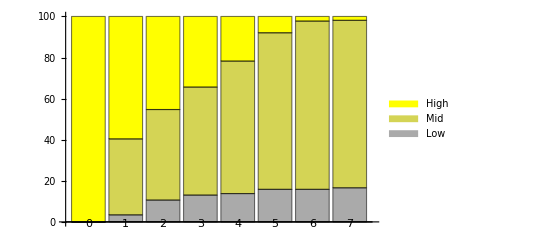

```mathematica
baryfphigh=BarChart[avgyfplow,ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Yellow},.5],Yellow},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}]
```

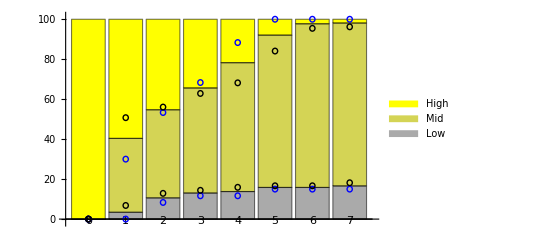

```mathematica
errorGraphicsyfphigh=Graphics[Table[With[{x=i,ymid630=N[100*exp630transition[[4,All,2]]][[i]]+N[100*exp630transition[[4,All,1]]][[i]],ymid227=N[100*exp227transition[[4,All,2]]][[i]]+N[100*exp227transition[[4,All,1]]][[i]],ylow630=N[100*exp630transition[[4,All,1]]][[i]],ylow227=N[100*exp227transition[[4,All,1]]][[i]]},
{{Blue,Circle[{x,ymid630},{0.07,1.4}]},{Blue,Circle[{x,ylow630},{0.07,1.4}]},{Black,Circle[{x,ymid227},{0.07,1.4}]},{Black,Circle[{x,ylow227},{0.07,1.4}]}}],{i,Length[avg]}]
];


(*Combine the bar chart with error bars*)
Show[baryfphigh,errorGraphicsyfphigh]
```